```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
ρ[t_,m_]:=ρ[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=
Module[{J=Inverse[β[ω,δ,t,ϵ,m]],A:=Inverse[β[ω,δ,t,ϵ,m]],T:=T[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,30000];J=J]
```

```mathematica
LEFT1[ω_,δ_,t_,ϵ_,m_]:=LEFT1[ω,δ,t,ϵ,m]=
Module[{J=Inverse[β[ω,δ,t,ϵ,m]],A:=Inverse[β[ω,δ,t,ϵ,m]],T:=T[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,30100];J=J]
```

```mathematica
Abs[Tr[LEFT[4,0.001,1,0,10]-LEFT1[4,0.001,1,0,10]]]
```

0.

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[1,m].LEFT[ω,δ,t,ϵ,m].T[1,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[1,m].LEFT[ω,δ,t,ϵ,m].T[1,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[1,m].SR[ω,δ,t,ϵ,m].T[1,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[1,m].SL[ω,δ,t,ϵ,m].T[1,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m].T[1,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].T[1,m].grr[ω,δ,t,ϵ,m].T[1,m]-T[1,m].GNON[ω,δ,t,ϵ,m].T[1,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[0,0.001,1,0,20]
```

19.9989

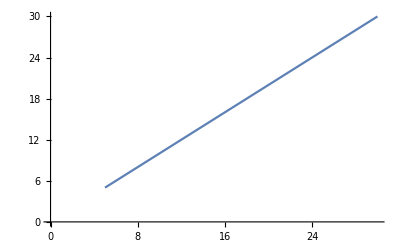

```mathematica
ListLinePlot[Table[{m,tr[0,0.001,1,0,m]},{m,Range[5,30,1]}]]
```

```mathematica
β[ω,δ,t,ϵ,7]
```

{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ,m],T=ρ[1,m]},
sl1=Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},
Inverse[IdentityMatrix[m]-c.ConjugateTranspose[T].J.T].c],100]; J=J];Il1:=Inverse[IdentityMatrix[m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

```mathematica
tr1[0,0.001,1,0,1,7]
```

2.1736

```mathematica
Δ[N_]:=Mean[Table[tr1[0,0.001,1,0,1,7],N]]-Mean[Table[tr1[0,0.001,1,0,1,7],N+100]]
```

```mathematica
Timing[Δ[10000]]
```

{105.891,-0.00944602}

```mathematica
Timing[Δ[1500]]
```

{2.85535,-0.0380199}

```mathematica
Table[{N,Δ[N]},{N,Range[2000,7000,250]}]
```

{{2000,0.0136092},{2250,-0.017373},{2500,0.00529594},{2750,0.000804197},{3000,-0.0200959},{3250,-0.000776592},{3500,0.00343924},{3750,-0.0184435},{4000,-0.00491249},{4250,-0.000909281},{4500,0.00570144},{4750,0.00934203},{5000,-0.00828602},{5250,-0.00497504},{5500,-0.00162514},{5750,-0.00462665},{6000,-0.00522035},{6250,-0.00628967},{6500,-0.0101624},{6750,0.00680909},{7000,0.00780073}}

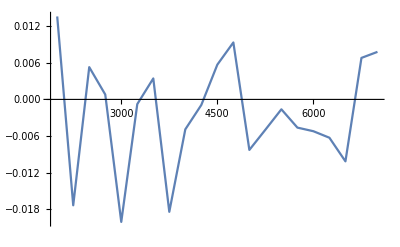

```mathematica
ListPlot[%72,Joined->True]
```

```mathematica
Table[{N,Δ[N]},{N,Range[7000,12000,250]}]
```

{{7000,-0.00467514},{7250,0.00582886},{7500,0.00430823},{7750,0.00282057},{8000,0.0105674},{8250,-0.00563672},{8500,0.00237233},{8750,0.000187026},{9000,-0.00346757},{9250,-0.00555846},{9500,0.00314593},{9750,-0.0000782205},{10000,0.00269121},{10250,0.00440384},{10500,-0.00611075},{10750,0.00835788},{11000,0.00213166},{11250,0.00318283},{11500,0.00178784},{11750,0.00352215},{12000,0.00177993}}

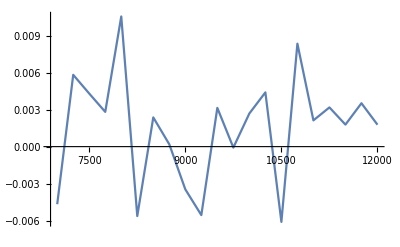

```mathematica
ListPlot[%74,Joined->True]
```

```mathematica
Δ[N_]:=Mean[Table[tr1[0,0.001,1,0,1,8],N]]-Mean[Table[tr1[0,0.001,1,0,1,8],N+100]]
```

```mathematica
Table[{N,Δ[N,8]},{N,Range[2000,12000,250]}]
```

{{2000,0.00347232},{2250,0.00549279},{2500,0.0110283},{2750,0.00487617},{3000,0.00878879},{3250,0.001449},{3500,0.00252018},{3750,0.00392573},{4000,0.00166287},{4250,0.0129048},{4500,0.00961971},{4750,0.0141659},{5000,0.018278},{5250,0.00702607},{5500,0.0231622},{5750,0.00126036},{6000,0.0016194},{6250,0.00628577},{6500,0.0120722},{6750,0.00550815},{7000,0.00227183},{7250,0.00371161},{7500,0.00717969},{7750,0.0046891},{8000,0.00284488},{8250,0.0101267},{8500,0.00768617},{8750,0.00262882},{9000,0.00459261},{9250,0.00130262},{9500,0.0045764},{9750,0.00770939},{10000,0.00104946},{10250,0.00544057},{10500,0.00157463},{10750,0.00631217},{11000,0.0130854},{11250,0.00956795},{11500,0.0120992},{11750,0.00519906},{12000,0.00663116}}

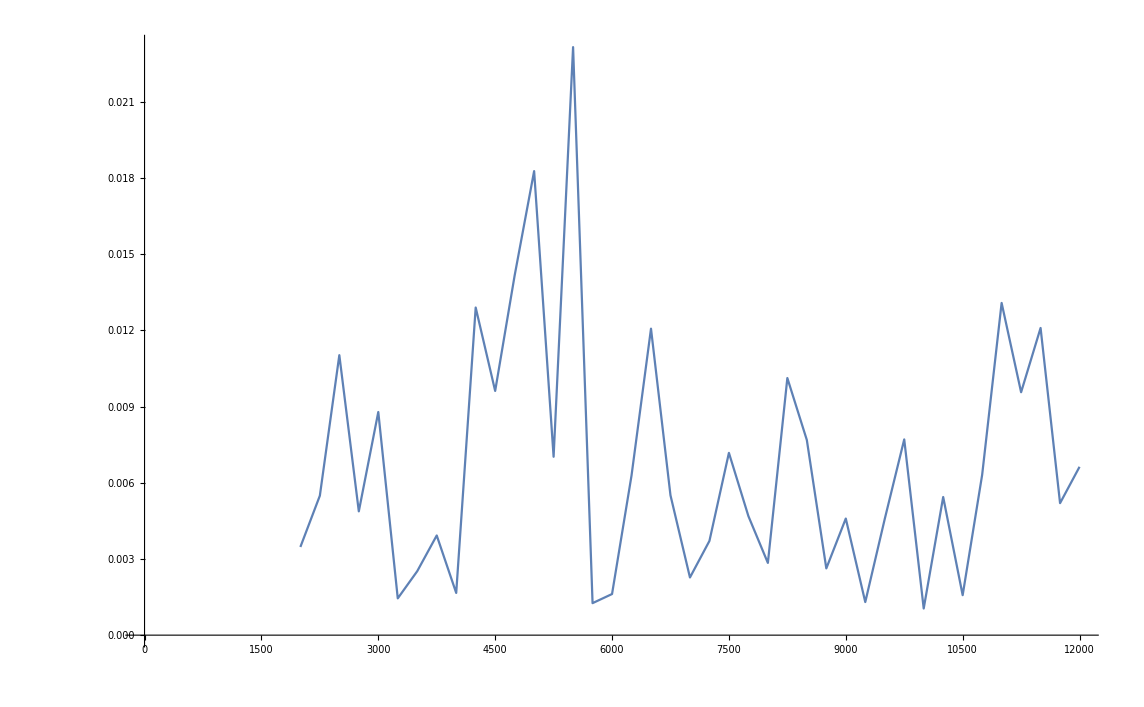

```mathematica
ListPlot[%83,Joined->True]
```

```mathematica
Δ[N_,m_]:=Δ[N,m]=Abs[Mean[Table[tr1[0,0.001,1,0,1,m],N]]-Mean[Table[tr1[0,0.001,1,0,1,m],N+100]]]
```

```mathematica
Table[{N,m,Δ[N,m]},{m,Range[3,10,1]},{N,Range[2000,12000,250]}]
```

{{{2000,3,9.30243},{2250,3,2.31383},{2500,3,19.0857},{2750,3,8.01103},{3000,3,24.0346},{3250,3,2.20058},{3500,3,8.74918},{3750,3,2.62103},{4000,3,9.76109},{4250,3,4.61308},{4500,3,0.118553},{4750,3,12.0795},{5000,3,5.73395},{5250,3,7.99786},{5500,3,5.56459},{5750,3,0.304384},{6000,3,4.92322},{6250,3,10.4606},{6500,3,20.3987},{6750,3,5.1897},{7000,3,7.80327},{7250,3,4.41395},{7500,3,1.02469},{7750,3,2.19385},{8000,3,2.95197},{8250,3,3.43972},{8500,3,3.02834},{8750,3,10.4724},{9000,3,13.3271},{9250,3,17.3736},{9500,3,7.80179},{9750,3,0.140697},{10000,3,7.83925},{10250,3,10.0288},{10500,3,1.99096},{10750,3,10.1523},{11000,3,15.1721},{11250,3,1.75693},{11500,3,5.35142},{11750,3,4.1116},{12000,3,10.4301}},{{2000,4,93.3988},{2250,4,3.35668},{2500,4,66.0964},{2750,4,2.2826},{3000,4,1.56051},{3250,4,11.6089},{3500,4,15.3163},{3750,4,1.69803},{4000,4,13.0561},{4250,4,9.16701},{4500,4,15.9317},{4750,4,4.90174},{5000,4,13.8467},{5250,4,17.3285},{5500,4,12.634},{5750,4,23.828},{6000,4,2.35296},{6250,4,14.2338},{6500,4,15.8204},{6750,4,9.98141},{7000,4,4.048},{7250,4,3.56519},{7500,4,17.869},{7750,4,31.1005},{8000,4,24.0655},{8250,4,2.27532},{8500,4,4.5887},{8750,4,5.26545},{9000,4,2.20813},{9250,4,11.6148},{9500,4,1.25845},{9750,4,13.3287},{10000,4,5.99566},{10250,4,4.27837},{10500,4,29.89},{10750,4,6.62858},{11000,4,10.1505},{11250,4,9.52399},{11500,4,7.35558},{11750,4,6.47562},{12000,4,5.64616}},{{2000,5,0.0241921},{2250,5,0.00599877},{2500,5,0.014823},{2750,5,0.0253419},{3000,5,0.00229356},{3250,5,0.0112251},{3500,5,0.0226934},{3750,5,0.00909116},{4000,5,0.0181729},{4250,5,0.0130192},{4500,5,0.00720836},{4750,5,0.0068842},{5000,5,0.040327},{5250,5,0.0158446},{5500,5,0.0441217},{5750,5,0.0221502},{6000,5,0.0260259},{6250,5,0.0127342},{6500,5,0.024605},{6750,5,0.0015999},{7000,5,0.0122699},{7250,5,0.00514238},{7500,5,0.00405878},{7750,5,0.0128796},{8000,5,0.0156768},{8250,5,0.00640234},{8500,5,0.00381572},{8750,5,0.0159526},{9000,5,0.0072103},{9250,5,0.00676265},{9500,5,0.00801386},{9750,5,0.00714994},{10000,5,0.00659107},{10250,5,0.0254273},{10500,5,0.00972737},{10750,5,0.00814021},{11000,5,0.00549503},{11250,5,0.00706838},{11500,5,0.00430372},{11750,5,0.0123076},{12000,5,0.000704127}},{{2000,6,0.111075},{2250,6,0.0678589},{2500,6,0.00329168},{2750,6,0.0290139},{3000,6,0.00184631},{3250,6,0.00853161},{3500,6,0.0564513},{3750,6,0.0238111},{4000,6,0.0123339},{4250,6,0.0114291},{4500,6,0.00869978},{4750,6,0.0383633},{5000,6,0.0140893},{5250,6,0.0348791},{5500,6,0.0105118},{5750,6,0.0128641},{6000,6,0.0525338},{6250,6,0.0313447},{6500,6,0.00404835},{6750,6,0.0219767},{7000,6,0.0333997},{7250,6,0.0163472},{7500,6,0.00768669},{7750,6,0.0224992},{8000,6,0.0105702},{8250,6,0.0228999},{8500,6,0.0105082},{8750,6,0.0271694},{9000,6,0.00693444},{9250,6,0.00502802},{9500,6,0.0221748},{9750,6,0.00752469},{10000,6,0.000711085},{10250,6,0.004487},{10500,6,0.00667347},{10750,6,0.00681417},{11000,6,0.00609194},{11250,6,0.01911},{11500,6,0.00433814},{11750,6,0.0126554},{12000,6,0.0293165}},{{2000,7,0.114957},{2250,7,0.00554221},{2500,7,0.0499457},{2750,7,0.0190918},{3000,7,0.0136189},{3250,7,0.0104487},{3500,7,0.0203973},{3750,7,0.0821801},{4000,7,0.0469502},{4250,7,0.017573},{4500,7,0.0543118},{4750,7,0.0199953},{5000,7,0.0266713},{5250,7,0.0462382},{5500,7,0.056787},{5750,7,0.0265722},{6000,7,0.0272312},{6250,7,0.0280527},{6500,7,0.0161544},{6750,7,0.0276336},{7000,7,0.0298729},{7250,7,0.0157391},{7500,7,0.00888423},{7750,7,0.011353},{8000,7,0.0437343},{8250,7,0.0149988},{8500,7,0.0591026},{8750,7,0.00776748},{9000,7,0.0102289},{9250,7,0.0503679},{9500,7,0.0814604},{9750,7,0.0469314},{10000,7,0.00987883},{10250,7,0.032353},{10500,7,0.0267338},{10750,7,0.00747703},{11000,7,0.0111458},{11250,7,0.0301397},{11500,7,0.00221763},{11750,7,0.00505488},{12000,7,0.00415737}},{{2000,8,0.0273012},{2250,8,0.10258},{2500,8,0.00405664},{2750,8,0.0208793},{3000,8,0.0596091},{3250,8,0.0971291},{3500,8,0.030724},{3750,8,0.0037324},{4000,8,0.0143177},{4250,8,0.0138582},{4500,8,0.0463751},{4750,8,0.0133372},{5000,8,0.0395451},{5250,8,0.0298296},{5500,8,0.0341436},{5750,8,0.0676974},{6000,8,0.00467365},{6250,8,0.0181499},{6500,8,0.0326451},{6750,8,0.0213833},{7000,8,0.00256919},{7250,8,0.0590916},{7500,8,0.0263379},{7750,8,0.0383959},{8000,8,0.0116752},{8250,8,0.0663542},{8500,8,0.00534331},{8750,8,0.0412911},{9000,8,0.045785},{9250,8,0.0235973},{9500,8,0.0300224},{9750,8,0.00355135},{10000,8,0.0136811},{10250,8,0.0127992},{10500,8,0.003263},{10750,8,0.00238071},{11000,8,0.00865392},{11250,8,0.00756948},{11500,8,0.0527884},{11750,8,0.0666382},{12000,8,0.0052315}},{{2000,9,0.15669},{2250,9,0.00689029},{2500,9,0.0806165},{2750,9,0.0342012},{3000,9,0.049245},{3250,9,0.0051023},{3500,9,0.0153554},{3750,9,0.0186486},{4000,9,0.0361074},{4250,9,0.0560027},{4500,9,0.0235102},{4750,9,0.00141185},{5000,9,0.0352683},{5250,9,0.033705},{5500,9,0.071234},{5750,9,0.0615254},{6000,9,0.024774},{6250,9,0.042415},{6500,9,0.0163132},{6750,9,0.0303063},{7000,9,0.0188802},{7250,9,0.0116432},{7500,9,0.0332502},{7750,9,0.0179621},{8000,9,0.0277347},{8250,9,0.0308249},{8500,9,0.0139179},{8750,9,0.00296269},{9000,9,0.0380782},{9250,9,0.0256469},{9500,9,0.0390001},{9750,9,0.0161655},{10000,9,0.0294838},{10250,9,0.0170895},{10500,9,0.0154896},{10750,9,0.0736895},{11000,9,0.00909196},{11250,9,0.00851964},{11500,9,0.0211873},{11750,9,0.0639511},{12000,9,0.00414415}},{{2000,10,0.053979},{2250,10,0.131599},{2500,10,0.0390637},{2750,10,0.146178},{3000,10,0.0724419},{3250,10,0.128418},{3500,10,0.0612038},{3750,10,0.0454806},{4000,10,0.0558078},{4250,10,0.0310875},{4500,10,0.0332625},{4750,10,0.0385868},{5000,10,0.0478256},{5250,10,0.0303752},{5500,10,0.00817589},{5750,10,0.0089139},{6000,10,0.0202695},{6250,10,0.0360341},{6500,10,0.0904909},{6750,10,0.0392063},{7000,10,0.0905141},{7250,10,0.0389655},{7500,10,0.035406},{7750,10,0.0952242},{8000,10,0.0023239},{8250,10,0.0263438},{8500,10,0.00495362},{8750,10,0.0405393},{9000,10,0.00328298},{9250,10,0.00594645},{9500,10,0.0162241},{9750,10,0.0138983},{10000,10,0.0392735},{10250,10,0.057871},{10500,10,0.0426141},{10750,10,0.0131298},{11000,10,0.0217804},{11250,10,0.00811817},{11500,10,0.00253359},{11750,10,0.119759},{12000,10,0.0453741}}}

```mathematica
Δ[3000,8]
```

0.0596091

```mathematica
F[m_]:=Table[{m,N,Δ[N,m]},{N,Range[2000,12000,250]}]
```

```mathematica
Range[3,20,1]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Map[F,%106][[18]]
```

{{20,2000,0.0981333},{20,2250,0.62417},{20,2500,0.214362},{20,2750,0.106852},{20,3000,0.0900812},{20,3250,0.135948},{20,3500,0.110047},{20,3750,0.359808},{20,4000,0.00870883},{20,4250,0.0601324},{20,4500,0.158687},{20,4750,0.21705},{20,5000,0.02735},{20,5250,0.163847},{20,5500,0.162923},{20,5750,0.0281921},{20,6000,0.138215},{20,6250,0.263754},{20,6500,0.355161},{20,6750,0.269588},{20,7000,0.0689835},{20,7250,0.084406},{20,7500,0.0244545},{20,7750,0.0524864},{20,8000,0.0350397},{20,8250,0.142425},{20,8500,0.047593},{20,8750,0.230704},{20,9000,0.0163123},{20,9250,0.0132378},{20,9500,0.0724957},{20,9750,0.0113594},{20,10000,0.0171708},{20,10250,0.140486},{20,10500,0.0705926},{20,10750,0.265231},{20,11000,0.121412},{20,11250,0.0713726},{20,11500,0.0458838},{20,11750,0.0881464},{20,12000,0.0877031}}

```mathematica
Δ[100000,20]
```

0.0643456

```mathematica
Δ[1000000,20]
```

0.0160015